# Over Constrained method

## Start

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

```mathematica
packageDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"pyramid1d`"
<<"pyramidalCyclope1D`"
```

```mathematica
noteBookMode="OverConstrained";
```

## Test Points {line1, line2, pyrf12}

```mathematica
(* We create test points for compilation test *)
line1=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1,30}],1];
line2=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1-1,30-1}],1];
ListPlot[{line1, line2},Joined->True,PlotMarkers->Automatic,PlotRange->All,PlotLabel->"Test Points",PlotLegends->{"ia","ib"}];
```

```mathematica
(*generate functions of pyramid with pyrFuncGen*)
(* input-> {original points, number of levels}*)
(* Output-> {functions f and df for n+1 levels} *)
pyrf1=pyrFuncGen[line1,3];
pyrf2=pyrFuncGen[line2,3];
pyrf12=Flatten[{pyrf1, pyrf2}, {{2},{1},{3}}];

Plot[{pyrf12[[4,1,1]][x],pyrf12[[4,2,1]][x]},{x,1,30}];
```

## Pyramidal Flow 1D (PyrFlow1D)

### PyrUpgrade1D

```mathematica
(* Function to update values of v1 and v2 with Over Constrained standards *)
(* Any value that does not meets the constraints becomes 0 *)

(* Input-> {{initial values for v1, v2 and status, and counter e}, pixel of interest, {functions f1, df1, f2, df2}, threshold for magnitude error}*)
(* Output-> {new values for v1, v2 and status and e} *)

PyrUpgrade1D[{v1_,v2_,status_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"OverConstrained"]:=Block[{p1, p2, c,d1,d2,dv1,dv2},(

p1=p0-v1;
p2=p0+v2;

c = (fline1[p0]+fline2[p0])/2;
d1=dfline1[p1];
d2=dfline2[p2];

(* d1 and d2 have to be the same sign in every iteration *)
If[d1*d2 <0, Return[{0,0,"sign"}]];

(* magnitude needs to be bigger than threshold every iteration *)
If[(Abs[d1]<threshold||Abs[d2]<threshold ),Return[{0,0,"mag"}]];

(* Change of sign during iteration *)
If[(dfline1[p0]*d1<0||dfline2[p0]*d2<0),Return[{0,0,"flip"}]];


(* dv1,dv2 : step from last {v1,v2} to new {v1,v2} *)
{dv1,dv2}= {(fline1[p1]-c)/d1,(c-fline2[p2])/d2};

(* status: "OK" -> solution respects constraints,  errors: "sign", "mag", "flip" *)
(* status: "converged" -> we converged!! *)
{v1+dv1,v2+dv2,If[Norm[{dv1,dv2}]<0.001,"converged","ok"]}
)];

(* No other solution will be calculated when status records an error message in this pyramidal level*)
PyrUpgrade1D[{v1_,v2_,"sign"},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"OverConstrained"]:={0,0,"sign"};

PyrUpgrade1D[{v1_,v2_,"mag"},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"OverConstrained"]:={0,0,"mag"};

PyrUpgrade1D[{v1_,v2_,"flip"},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"OverConstrained"]:={0,0,"flip"};
```

### Test

```mathematica
(* initial values *)
{v1, v2}={0.,0.};
status="ok";
i=0;
p=17;
```

```mathematica
(*Test for PyrUpgrade1D, manual test to iterate multiple times*)
(* n is the level of pyramid *)
n=2;
{v1,v2,status}=PyrUpgrade1D[{v1,v2,status},p, pyrf12[[n]],0.01,noteBookMode]
```

{0.389495,1.06145,ok}

```mathematica
(* see *)
seePlot[p,2,{v1,v2},pyrf12[[n]]];
```

### PyrFlow1D

```mathematica
(* Function to find solutions for all levels of pyramid {l1,l2,l3,l4,...} or {l1} *)
(* Input-> {number of iterations, pixel of interests, pyrfunctions,threshold *)
(* Output-> {v1, v2,status}*)
PyrFlow1D[i_, p0_, pyrfunctions_,threshold_,"OverConstrained"]:=Block[{v1, v2,c,status},(

c=Length[pyrfunctions]; (* number of levels *)

{v1, v2,status}={0.,0.,"ok"};

Do[
(* compute at this scale, using current motion estimate *)
{v1,v2,status}=Nest[PyrUpgrade1D[#,p0, pyrfunctions[[-f]],threshold*2^(-c+1),"OverConstrained"]&,{v1,v2,status},i];

c=c-1

,{f,1,Length[pyrfunctions]}];

{v1, v2,status}
)];
```

#### Test

0.01*2^(-m) depends on m to update the error depending on the highest resolution scale

```mathematica
(* Initializing values *)
{v1, v2}={0.,0.};
i=10;
p=19;

(* m-> max lvl, n-> min lvl *)
m=3;
n=3;

(*PyrFlow1D solution*)
{v1,v2,status}=PyrFlow1D[i, p,pyrf12[[m;;n]],0.0001*2^(-m+1),"OverConstrained"]
{Total[{v1,v2}],status}
```

{0.472379,0.480451,converged}

{0.95283,converged}

```mathematica
(* see *)
seePlot[p,2,{v1,v2},pyrf12[[m]]];
```

## Graphics for All pixels

### All Pixel Graphics

#### Test

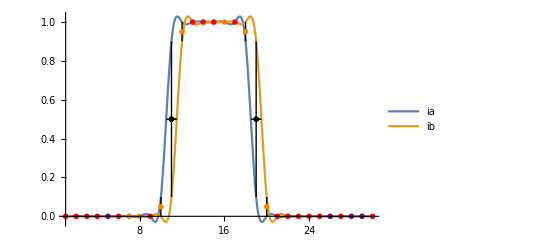

```mathematica
tes1=lineTest[Range[1,Length[line1]],pyrf12[[1;;3]],0.001,noteBookMode];
seeAllLine[Range[1,30],pyrf12[[1;;3]],0.001,noteBookMode]
```

## Graphics for One pixel

```mathematica
(* Function to find solutions for all levels of pyramid {l1,l2,l3,l4,...} or {l1} *)
(* Input-> {number of iterations, pixel of interests, pyrfunctions,threshold *)
(* Output-> {v1, v2,status}*)
PyrFlow1DIter[i_, p0_,v0_, pyrfunctions_,threshold_,"OverConstrained"]:=Block[{v1, v2,c,status,iterTable},(

c=Length[pyrfunctions]; (* number of levels *)

{v1, v2}=v0;
status="ok";

Table[
(* compute at this scale, using current motion estimate *)

iterTable=Table[
(*index of pyrfunction works only if fed the right range of pyrfunctions*)
{v1,v2,status}=PyrUpgrade1D[{v1,v2,status},p0, pyrfunctions[[-f]],threshold*2^(-c+1),"OverConstrained"];

{v1,v2,status}
,{j,1,i}];

c=c-1;
iterTable
,{f,1,Length[pyrfunctions]}]

)];
```

#### Test

```mathematica
iter=PyrFlow1DIter[10, 11,{0.,0.}, pyrf12[[1 ;;1]],0.001,"OverConstrained"]
```

{{{0.722992,0.723034,ok},{0.487114,0.487118,ok},{0.499998,0.500007,ok},{0.499996,0.500004,converged},{0.499996,0.500004,converged},{0.499996,0.500004,converged},{0.499996,0.500004,converged},{0.499996,0.500004,converged},{0.499996,0.500004,converged},{0.499996,0.500004,converged}}}